{{θ→InterpolatingFunction[{{0., 4000.}}, <>]}}

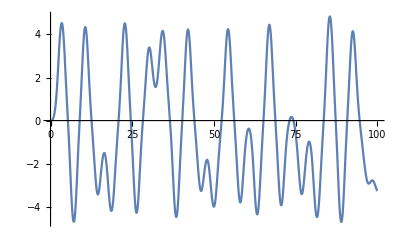

```mathematica
sol=
NDSolve[
{-0.1θ'[t]+1Sin[θ[t]]-0.2(θ[t]-3Sin[t])==0.5θ''[t],
θ[0]==0,θ'[0]==0},θ,{t,0,4000}]
Plot[θ[t]/.sol,{t,0,100}]
```

```mathematica
{{θ->InterpolatingFunction[{{0., 2504.55}}, <>]}}
```

InterpolatingFunction::noinfo: 输入表达式 InterpolatingFunction[{{0., 4000.}}, <>] 包含的信息不足，无法解释结果.

General::stop: 在本次计算中，StyleBox[RowBox[{\"ReplaceAll\", \"::\", \"reps\"}], \"MessageName\"] 的进一步输出将被抑制.